# Currency Areas and Voluntary Transfers Four State Case Picard Worrall 12-08-2020

Define parameters and their aggregates

```mathematica
μ=.99;(*Cobb Douglas preference for money *) 
θvar=μ/(1-μ); ξ=μ^μ(1-μ)^(1-μ);
θ=5; (*elasticity of substitution between labor services*)
M0w=1; (*world money supply*)
nbS=4;  (*number of symmetric shocks*)
a={1,1,z,z}; (*vector of home shock*)
as={1,z,1,z};(*vector of foreign shock*)
πs={π0,1-π0,1-π0,π0}; (*vector of probabilities of iid shock*)
A[s_]:=((1/2)^σ a[[s]]^(1-σ)+(1/2)^σ as[[s]]^(1-σ))^(1/(1-σ)); (*shock aggregate, see paper*)
b[s_]:=a[[s]]^(1-σ)/(1/2 a[[s]]^(1-σ)+1/2 as[[s]]^(1-σ)); (*shock aggregate, see paper*)
bs[s_]:=as[[s]]^(1-σ)/(1/2 a[[s]]^(1-σ)+1/2 as[[s]]^(1-σ)) ; (* shock aggregate, see paper *)
```

## Currency area

Letter c indicates currency area. c0 a currency area with no transfers and co a currency area with optimal transfers.
Define income Yc, aggregate consumption Xc, wage Wc, utility Uc, expected utility EUc, vector of optimal transfers vTcopt and expected utility with those optimal transfers.

```mathematica
Yc[s_]:= 1/2 θvar b[s] M0w;
Xc[s_,W_, Ts_]:=ξ/μ (1/2 θvar b[s] M0w +Ts)/(A[s]W);
XcoverW[s_, Ts_]:=ξ/μ (1/2 θvar b[s] M0w +Ts)/A[s];
Wc[vT_]:=((∑_(s=1)^4 πs[[s]] Yc[s]^2)/(ξ∑_(s=1)^4 πs[[s]](XcoverW[s,vT[[s]]]^-γ Yc[s]/A[s])))^(1/(1+γ));
vTcopt=Table[1/4 θvar (bs[s]-b[s])M0w,{s,1,4}];
Uc[s_,W_,Ts_]:=(Xc[s,W, Ts])^(1-γ)/(1-γ)-1/2(Yc[s]/W)^2;
EUc[W_,vT_]:=∑_(s=1)^4 πs[[s]]Uc[s,W,vT[[s]]];
EUopt:=EUc[Wc[vTcopt],vTcopt];
```

## Flexible exchange rate with no transfers

A letter f denotes a flexible exchange rate, f0 a flexible exchange rate with no transfers.
Define country money supply M0, income Yf0, exchange rate ϵ0, aggregate consumption Xf0, wage Wf0, utility Uf0 and expected utility EUf0

```mathematica
M0=M0w/2;
Yf0[s_]:=θvar M0;
ϵ0[s_]:=(b[s]/bs[s])^(-1/σ);
B0[s_]:=(1/2 b[s]+1/2 bs[s] ϵ0[s]^(1-σ))^(1/(1-σ));
Xf0[s_,W_]:=ξ/μ(θvar M0)/(A[s] W B0[s]);
Xf0overW[s_]:=ξ/μ(θvar M0)/(A[s]  B0[s]);

Wf0:=((∑_(s=1)^4 πs[[s]](Yf0[s])^2)/(ξ∑_(s=1)^4 πs[[s]](Xf0overW[s]^-γ Yf0[s]/(A[s]B0[s]))))^(1/(1+γ));
Uf0[s_,W_]:=(Xf0[s,W])^(1-γ)/(1-γ)-1/2(Yf0[s]/W)^2;

EUf0:=∑_(s=1)^4 πs[[s]]Uf0[s,Wf0];
```

#### Define the difference in expected utility between currency area with optimal transfers and flexible exchange rate without transfers.

```mathematica
DiffEUoptf0[z_,σ_,γ_,π0_]=EUopt-EUf0;
```

### Flexible exchange rate with transfers

Define country money supply M0, income Yf, exchange rate ϵ, aggregate consumption Xf, wage Wf, utility Uf and expected utility EUf.
Ignore warning messages about Part function

```mathematica
M0=M0w/2;

Yf[s_,Ts_]:=θvar M0-Ts;
ϵ0[s_]:=(a[[s]]^(1-σ)/as[[s]]^(1-σ))^(-1/σ);
ϵ[s_,Ts1_?NumberQ,z1_?NumberQ,σ1_?NumberQ,γ1_?NumberQ]:=Module[{ϵ,f,init},f=Evaluate[ϵ-(a[[s]]^(1-σ)/as[[s]]^(1-σ))^(-1/σ)((1-Ts/(θvar M0))/(1+Ts/(ϵ  θvar M0)))^(1/σ)]/.{Ts->Ts1,z->z1,σ->σ1,γ->γ1};
init=Evaluate[(b[s]/bs[s])^(-1/σ)]/.{Ts->Ts1,z->z1,σ->σ1,γ->γ1};
ϵ/.FindRoot[f,{ϵ,.9*init,init}]
];

B[s_,Ts_,zx_,σx_,γ_]:=(1/2 b[s]+1/2 bs[s]*ϵ[s,Ts,z,σ,γ]^(1-σ))^(1/(1-σ))/. {z->zx, σ->σx};


Xf[s_,W_,Ts_,zx_,σx_,γ_]:=Evaluate[ξ/μ((θvar M0)/(((1/2)^σ a[[s]]^(1-σ)+(1/2)^σ as[[s]]^(1-σ))^(1/(1-σ)) W B[s,Ts,z,σ,γ]))]/. {z->zx, σ->σx}//Quiet;

XfoverW[s_,Ts_,zx_,σx_,γ_]:=Evaluate[ξ/μ((θvar M0)/(((1/2)^σ a[[s]]^(1-σ)+(1/2)^σ as[[s]]^(1-σ))^(1/(1-σ))  B[s,Ts,z,σ,γ]))]/. {z->zx, σ->σx}//Quiet;
Wf[vT_,zx_,σx_,γ_,π0x_]:=Evaluate[((∑_(s=1)^4 πs[[s]](Yf[s,vT[[s]]])^2)/(ξ∑_(s=1)^4 πs[[s]]( (XfoverW[s,vT[[s]],z,σ,γ]^-γ Yf[s,vT[[s]]])/(((1/2)^σ a[[s]]^(1-σ)+(1/2)^σ as[[s]]^(1-σ))^(1/(1-σ)) B0[s]))))^(1/(1+γ))]/. {z->zx, σ->σx, π0->π0x}//Quiet;

Uf[s_,W_,Ts_,z_,σ_,γ_]:=(Xf[s,W,Ts,z,σ,γ])^(1-γ)/(1-γ)-1/2(Yf[s,Ts]/W)^2;

EUf[W_,vT_,z_,σ_,γ_,π01_]:=∑_(s=1)^4 πs[[s]]Uf[s,W,vT[[s]],z,σ,γ]/.π0->π01;
```

### Critical discount factors

Compute the critical discount factors that sustain the optimal transfers and do not sustain any small transfer in the currency area   (δcd,δcu) and in the flexible exchange rate regime (δfd and δfu).

```mathematica
T00={0,0,0,0};  (* vector of zero  transfers *)
T01={0,10^-2,-10^-2,0}; (* vector of small transfers (tends to zero)*)
δcd:=1/(1+1/((Uc[3,Wc[T01],T00[[3]]]-Uc[3,Wc[T01],T01[[3]]])/(EUc[Wc[T01],T01]-EUc[Wc[T00],T00])));
δcu:=1/(1+1/((Uc[3,Wc[vTcopt],T00[[3]]]-Uc[3,Wc[vTcopt],vTcopt[[3]]])/(EUc[Wc[vTcopt],vTcopt]-EUc[Wc[T00],T00])));

δ1mδd[z_,σ_,γ_,π0_]:=(Uf[3,Wf[T01,z,σ,γ,π0],T00[[3]],z,σ,γ]-Uf[3,Wf[T01,z,σ,γ,π0],T01[[3]],z,σ,γ])/(EUf[Wf[T01,z,σ,γ,π0],T01,z,σ,γ,π0]-EUf[Wf[T00,z,σ,γ,π0],T00,z,σ,γ,π0]) ;(* intermediate step *)

δfd[z_,σ_,γ_,π0_]:=1/(1+1/δ1mδd[z,σ,γ,π0]);

δ1mδu[z_,σ_,γ_,π0_]:=(Uf[3,Wf[vTcopt,z,σ,γ,π0],T00[[3]],z,σ,γ]-Uf[3,Wf[vTcopt,z,σ,γ,π0],vTcopt[[3]],z,σ,γ])/(EUf[Wf[vTcopt,z,σ,γ,π0],vTcopt,z,σ,γ,π0]-EUf[Wf[T00,z,σ,γ,π0],T00,z,σ,γ,π0]); (* intermediate step *)
δfu[z_,σ_,γ_,π0_]:=1/(1+1/δ1mδu[z,σ,γ,π0]);
```

Compute the constrained transfers in currency area

```mathematica
δcd1[z_,σ_,γ_,π0_]=δcd;
δcu1[z_,σ_,γ_,π0_]=δcu;
constrtransferc[δ1_,z1_,σ1_,γ1_,π01_,T1_]:=Module[{T2={0,T1,-T1,0}},Uc[3,Wc[T2],T2[[3]]]-Uc[3,Wc[T2],T00[[3]]]+δ1/(1-δ1)(EUc[Wc[T2],T2]-EUc[Wc[T00],T00])/.{z->z1,σ->σ1,γ->γ1,π0->π01}
];

EU1c[δ1_,z1_,σ1_,γ1_,π01_]:=Module[
{r={z->z1,σ->σ1,γ->γ1,π0->π01},vTcopt1,vT1},
vTcopt1=vTcopt/.r;
Which[
δ1>=δcu1[z1,σ1,γ1,π01],EUc[Wc[vTcopt1],vTcopt1]/.r,
δ1<=δcd1[z1,σ1,γ1,π01],EUc[Wc[T00],T00]/.r,
True,vT1={0,T,-T,0}/.FindRoot[constrtransferc[δ1,z1,σ1,γ1,π01,T],{T,0.0001,-vTcopt1[[3]]}];
EUc[Wc[vT1],vT1]/.r
]]
```

Compute the constrained transfers in the flexible exchange rate system

```mathematica
δfu1[z1_,σ1_,γ1_,π01_]=δfu[z,σ,γ,π0] /.{z->z1,σ->σ1,γ->γ1,π0->π01};
δfd1[z1_,σ1_,γ1_,π01_]=δfd[z,σ,γ,π0] /.{z->z1,σ->σ1,γ->γ1,π0->π01};

constrtransferf[δ1_,z1_,σ1_,γ1_,π01_,T1_]:=Module[{T2={0,T1,-T1,0}},Uf[3,Wf[T2,z1,σ1,γ1,π01],T2[[3]],z1,σ1,γ1]-Uf[3,Wf[T2,z1,σ1,γ1,π01],T00[[3]],z1,σ1,γ1]+δ1/(1-δ1)(EUf[Wf[T2,z1,σ1,γ1,π01],T2,z1,σ1,γ1,π01]-EUf[Wf[T00,z1,σ1,γ1,π01],T00,z1,σ1,γ1,π01])/.{z->z1,σ->σ1,γ->γ1,π0->π01}
];
EU1f[δ1_,z1_,σ1_,γ1_,π01_]:=Module[
{r={z->z1,σ->σ1,γ->γ1,π0->π01},vTcopt1,vT1},
vTcopt1=vTcopt/.r;
T00={0,0,0,0};
Which[
δ1>=δfu1[z1,σ1,γ1,π01],EUf[Wf[vTcopt1,z1,σ1,γ1,π01],vTcopt1,z1,σ1,γ1,π01] /.r,
δ1<=δfd[z1,σ1,γ1,π01],EUf[Wf[T00,z1,σ1,γ1,π01],T00,z1,σ1,γ1,π01] /.r,
True,
vT1={0,T,-T,0}/.FindRoot[constrtransferf[δ1,z1,σ1,γ1,π01,T]/.r,{T,0.0001,-vTcopt1[[3]]}];
EUf[Wf[vT1,z1,σ1,γ1,π01],vT1,z1,σ1,γ1,π01]/.r
]];
```

#### Compare expected constrained utility levels

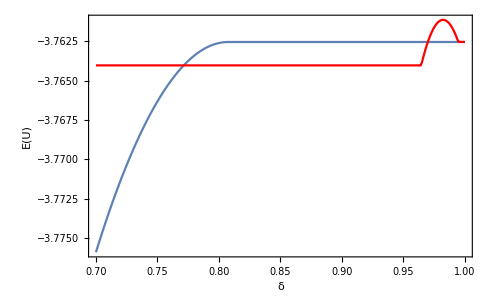

```mathematica
z0=.9;σ0=2.5;γ0=5;π00=1/2;
ThisString=(
"σ="<>ToString[σ0]<>
", θ="<>ToString[θ]<>
", γ="<>ToString[Chop[γ0]]<>
", μ="<>ToString[μ]<>
", z="<> ","<>ToString[z0]
);

ThisFrameLabel={
"δ",
"E(U)",
"E(U) and constrained transfers (Blue=Curr.Area, Red=Flexible Exch.)",
ThisString
};
imagesize=246;
lp1=ListPlot[ParallelTable[{δ,EU1c[δ,z0,σ0,γ0,π00]},{δ,0.7,1,.001}],Joined->True, PlotRange->All]; (* Note Parallel kernels invoked *)
lp2=ListPlot[ParallelTable[{δ,EU1f[δ,z0,σ0,γ0,π00]},{δ,0.7,1,.001}],Joined->True, PlotStyle->Red, PlotRange->All]; (* Note Parallel kernels invoked *)
Show[lp1,lp2, PlotRange->All,Frame->True,FrameLabel->ThisFrameLabel, ImageSize->imagesize*2]
```

Compute expected utility difference between currency area and flex. exch. rate

```mathematica
{z0,δ0,σ0,γ0}={.9,0.95,2,5};
ThisPlotPoints=30;
{zmin,zmax,σmin,σmax}={.8,.991,1.01,3.01};
π0=0.5;

ThisString=(
"δ="<>ToString[δ0]<>
", θ="<>ToString[θ]<>
", μ="<>ToString[μ]);
ThisFrameLabel={
"z",
"σ",
"Expected Utility Difference between Currency Area and Flex. Exch. Rate: \n fiscal union (bold line) and currency area with sustainable transfers (shaded area)",
ThisString
};

DEU1cf[z_,σ_,γ_]:=EU1c[δ0,z,σ,γ,0.5]-EU1f[δ0,z,σ,γ,0.5];
ptx=ParallelTable[ContourPlot[DEU1cf[z,σ,γ],{z,zmin,0.999},{σ,σmin,σmax},PlotPoints->ThisPlotPoints,Contours->{0},ContourStyle->GrayLevel[0.5],ContourShading->{None,{Gray,Opacity[.15]}}],{γ,{1.0001,2,3,4,5,6}}];

pty=Show[ParallelTable[ContourPlot[DiffEUoptf0[z,σ,γ,.5],{z,zmin,zmax},{σ,σmin,σmax}, Contours->{0},ContourShading->False, ContourStyle->GrayLevel[0.1]],{γ,{1.0001,2,3,4,5,6}}],PlotPoints->ThisPlotPoints*5, PlotRangePadding->{{0,0.009},{0, 0.1}}];
```

```mathematica
Figure 5
```

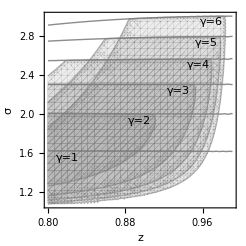

```mathematica
g6=Graphics[Text["γ=6", {0.9695,2.939}]];
g5=Graphics[ Text["γ=5", {0.9644,2.728}]];
g4=Graphics[Text["γ=4",{0.9557,2.50}]];
g3=Graphics[Text["γ=3",{0.9345,2.235}]];
g2=Graphics[Text["γ=2",{0.8945,1.926}]];
g1=Graphics[Text["γ=1",{0.82,1.55}]];

pl3=Show[pty, ptx,g1,g2,g3,g4,g5,g6, Frame->True,ImageSize->imagesize,FrameLabel->{{"σ",""},{"z",""}},FrameTicksStyle->Directive[Gray,10],PlotRange->All]
```